# LD Power Curves

## Moglabs 780 nm “780B”

7/17/19-7/18/19

```mathematica
powerNoFilter = {0.018,0.044,0.079,0.149,4,12.24,17.49,23.72,28.5,31.84};
current100 = {10,20,30,40,50,60,70,80,90,100};
```

```mathematica
powerFilter = {0.001,0.00195,0.0034,0.0057,1.8,7.84,12.85,18.26,21.75,24.28,25.85,25.88,26.45,26.38,25.77};
current150 = {10,20,30,40,50,60,70,80,90,100,110,120,130,140,150};
```

```mathematica
powerBareDiode = {0.005,0.014,0.023,0.035,0.052,0.078,0.120,0.188,0.294,0.449,0.670,0.98,1.41,1.976,2.693};
```

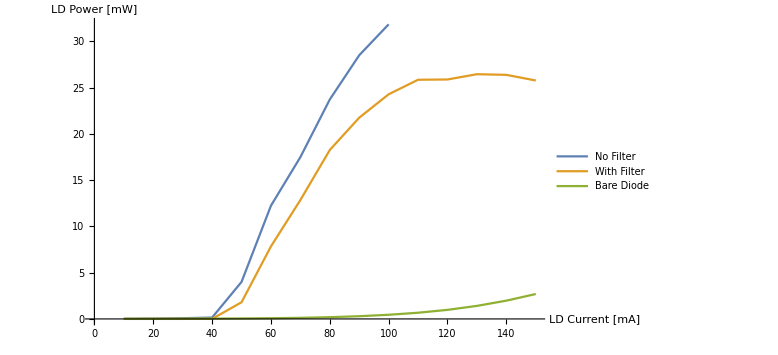

```mathematica
ListPlot[{Transpose@{current100,powerNoFilter},Transpose@{current150,powerFilter},Transpose@{current150,powerBareDiode}},Joined->True,AxesLabel->{"LD Current [mA]","LD Power [mW]"},PlotLegends->{"No Filter","With Filter","Bare Diode"},ImageSize->Large]
```

7/18/19

```mathematica
WignerD[{2,0,0},5.6*π/180]
```

0.985716

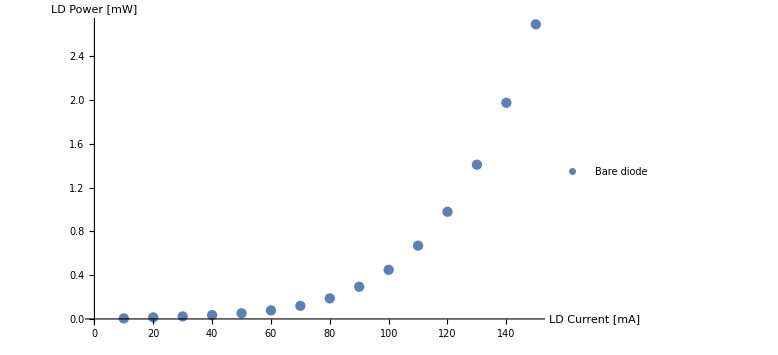

```mathematica
ListPlot[{Transpose@{current150,powerBareDiode}},AxesLabel->{"LD Current [mA]","LD Power [mW]"},PlotLegends->{"Bare diode"},ImageSize->Large]
```